```mathematica
f[e_,l_]:=1/(1-Exp[-e+I*l])
```

```mathematica
mult[e_]:=1/2(e+1)(e+2)
```

```mathematica
g[l_]:=1/(2π)E^(-I*n*l)*Product[f[e,l]^mult[e],{e,0,4}]
```

```mathematica
Plot3D[Abs[g[x+I y]]/.n->5,{x,-π,π},{y,-2,2},PlotRange->{0,10}]
```

-Graphics3D-

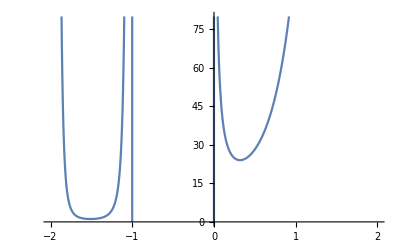

```mathematica
Plot[Re[g[I m]]/.n->5,{m,-2,2},PlotRange->{0,80}]
```

```mathematica
N[Minimize[{Re[g[-I m]]/.n->5,0>m>-1},m]]
```

{24.0319,{m→-0.318114}}

```mathematica
%[[2]]
```

{m→-0.318114}

```mathematica
mmin=m/.%
```

-0.318114

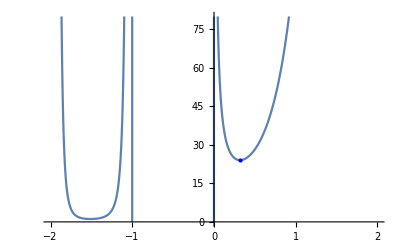

```mathematica
Plot[{Re[g[I m]]/.n->5},{m,-2,2},Epilog->{Blue,PointSize@Large,Point[{-mmin,24.031878206476605}]},PlotRange->{0,80}]
```

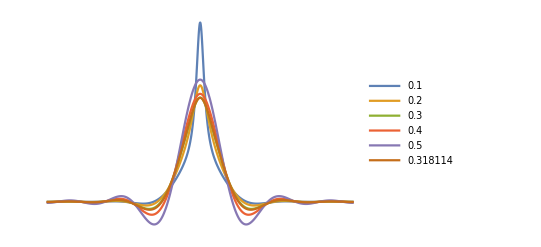

```mathematica
Plot[{Re[g[x+I*0.1]]/.n->5,Re[g[x+I*0.2]]/.n->5,Re[g[x+I*0.3]]/.n->5,Re[g[x+I*0.4]]/.n->5,Re[g[x+I*0.5]]/.n->5,Re[g[x+I*-mmin]]/.n->5},{x,-π,π},PlotRange->Full,PlotLegends->{0.1,0.2,0.3,0.4,0.5,-mmin},Axes->False]
```